```mathematica
D[a Integrate[Cos[x],{x,0,ArcTan[a]}]-Integrate[Sin[x],{x,0,ArcTan[a]}]-Integrate[Sin[x],{x,Pi/2,ArcTan[a]}]+a Integrate[Cos[x],{x,Pi/2,ArcTan[a]}],a]
```

-1-(2 a)/((1+a^2)^(3/2))-a^3/((1+a^2)^(3/2))+(3 a)/(√(1+a^2))+a (-a^2/((1+a^2)^(3/2))+1/(√(1+a^2)))

```mathematica
Simplify[-1-(2 a)/((1+a^2)^(3/2))-a^3/((1+a^2)^(3/2))+(3 a)/(√(1+a^2))+a (-a^2/((1+a^2)^(3/2))+1/(√(1+a^2)))]
```

-1+(2 a)/(√(1+a^2))

```mathematica
Solve[-1+(2 a)/(√(1+a^2))==0,a]
```

{{a→1/(√3)}}

```mathematica
D[-1+(2 a)/(√(1+a^2)),a]
```

```mathematica
-(2 a^2)/((1+a^2)^(3/2))+2/(√(1+a^2))/.{a->1/(√3)}
```

(3 √3)/4

```mathematica
f[a_]:=NIntegrate[Abs[Sin[x]-a Cos[x]],{x,0,Pi/2},AccuracyGoal->4];
```

```mathematica
f[1]
```

0.828427

```mathematica
Table[{i,f[i]},{i,-1,1,0.1}]
```

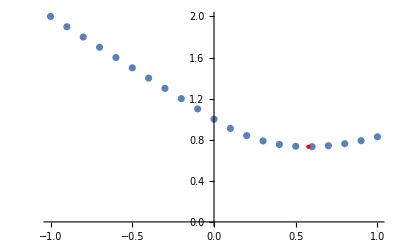

```mathematica
Show[ListPlot[{{-1.,2.0000000000000018},{-0.9,1.9000000000000017},{-0.8,1.800000000000002},{-0.7,1.7000000000000017},{-0.6,1.6000000000000016},{-0.5,1.5000000000000018},{-0.3999999999999999,1.400000000000001},{-0.29999999999999993,1.3000000000000014},{-0.19999999999999996,1.200000000000001},{-0.09999999999999998,1.1000000000000008},{0.,1.0000000000000009},{0.10000000000000009,0.9099758755902316},{0.20000000000000018,0.8396066896129128},{0.30000000000000004,0.7880613017821108},{0.40000000000000013,0.7540742016896237},{0.5,0.7360679774997902},{0.6000000000000001,0.7323806779590272},{0.7000000000000002,0.7412950389914079},{0.8,0.7612496949731403},{0.9000000000000001,0.7907248094147428},{1.,0.8284271247461908}}],Graphics[{Red,Point[{1/(√3),f[1/(√3)]}]}]]
```